Quantum 3-wave instability

Original authors of paper: Michael May, Hong Qin
Link to paper: https://journals.aps.org/pra/abstract/10.1103/PhysRevA.107.062204
Notebook by: Óscar Amaro (2024)

## Figure 1

```mathematica
(* equation 44 actually has a closed-form solution *)
Clear[ϵ,eq44]
eq44=(2ϵ^2(1-ϵ^2))/((1+ϵ^2)^2)Sum[ϵ^(2n)(2n(n+1)+1),{n,0,∞}]
eq44/.{ϵ->0.1}
```

-(2 ϵ^2 (1-ϵ^2))/((-1+ϵ^2)^3)

0.0204061

```mathematica
(* solve linearized differential equation for n1 *)
Clear[γQ,BQ,n1,τ]
DSolve[{n1''[τ]==n1[τ] γQ^2-BQ,n1[0]==0},n1[τ],τ]//Simplify
```

{{n1[τ]→(ⅇ^(-γQ τ) (-1+ⅇ^(γQ τ)) (BQ+(1+ⅇ^(γQ τ)) γQ^2 C[1]))/γQ^2}}

7.91872

4.01872

4.44089×10^-16

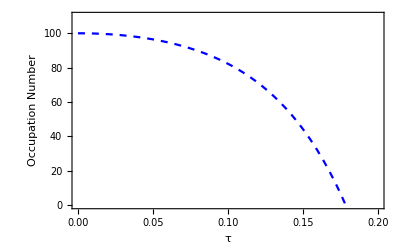

```mathematica
Clear[γQ,BQ,n1i,n2i,n3i,C1,δ10,eq51,δ1,ϵ]

δ1=δ10;

(* also in §C.Classical correspondence *)
(* quantum growth rate equation 47 *)
γQ=2Sqrt[n1i-n2i-n3i-1/2];
(* equation 48, "Since the growth of δ1 may be made arbitrarily small with 
, let us assume a constant variance such that BQ(τ ) = BQ(0) ≡ BQ" *)
BQ=2n1i(1+n2i+n3i)-2n2i n3i-6 δ1;

(* parameters in caption of figure 1 *)
{n1i,n2i,n3i}={100,10,3};
ϵ=0.1;
δ10=0.02040608101214162;
C1=-3.9;

(* equation 51 *)
eq51=BQ/γQ^2+C1  Exp[γQ τ]-(BQ/γQ^2+C1)Exp[-γQ τ];
(BQ/γQ^2)
(BQ/γQ^2+C1)
eq51/.{τ->0}

Plot[{100+eq51},{τ,0,0.2},PlotRange->{0,110},PlotStyle->{{Blue,Dashed},{Blue,Dashed}},Frame->True,FrameLabel->{"τ","Occupation Number"}]
```

## Matrix small examples

```mathematica
Clear[h,i,d,s2]
s2=3;
d=s2+1;
hi=DiagonalMatrix[Array[h,d,-1]];
H=RotateLeft[hi,1];
H[[-1,1]]=0;
H=H+Transpose[H];
H//MatrixForm
Eigenvalues[H]
```

(0 | h[0] | 0 | 0
h[0] | 0 | h[1] | 0
0 | h[1] | 0 | h[2]
0 | 0 | h[2] | 0)

{-(√(h[0]^2+h[1]^2+h[2]^2-√(-4 h[0]^2 h[2]^2+(-h[0]^2-h[1]^2-h[2]^2)^2)))/(√2),(√(h[0]^2+h[1]^2+h[2]^2-√(-4 h[0]^2 h[2]^2+(-h[0]^2-h[1]^2-h[2]^2)^2)))/(√2),-(√(h[0]^2+h[1]^2+h[2]^2+√(-4 h[0]^2 h[2]^2+(-h[0]^2-h[1]^2-h[2]^2)^2)))/(√2),(√(h[0]^2+h[1]^2+h[2]^2+√(-4 h[0]^2 h[2]^2+(-h[0]^2-h[1]^2-h[2]^2)^2)))/(√2)}

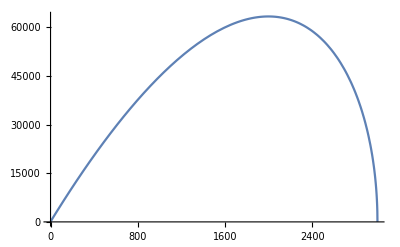

```mathematica
Clear[i,s2,s3]
s2=3000;s3=s2+1;
Plot[(Sqrt[(s2-i)(s3-s2+i+1)(i+1)]),{i,0,s2}]
```

```mathematica
Clear[i,j,s2,s3,hi,d,H,diag]
d=s2+1;

s2=3;s3=3;
hi[i_]:=Sqrt[(s2-i)(s3-s2+1+i)(i+1)]
diag=DiagonalMatrix[Table[hi[i],{i,0,s2}]];
H=RotateLeft[diag,-1];
H=H+Transpose[H];
H//MatrixForm
(*H=SparseArray[H];*)
eigs=Eigenvalues[H]//N;
eigs=Sort[eigs]
Differences[eigs]
```

(0 | √3 | 0 | 0
√3 | 0 | 2 √2 | 0
0 | 2 √2 | 0 | 3
0 | 0 | 3 | 0)

{-4.30627,-1.20665,1.20665,4.30627}

{3.09963,2.41329,3.09963}

```mathematica
(* this part of the computation can take some time ...*)
Clear[i,j,s2,s3,hi,d,H,eigs,eigsdiff]
d=s2+1;

s2=100;s3=100;
hi[i_]:=Sqrt[(s2-i)(s3-s2+1+i)(i+1)]
H=Table[KroneckerDelta[i,j+1]hi[i],{i,0,s2},{j,0,s2}];(*+KroneckerDelta[i+1,j]hi[j]*)
H=H+Transpose[H];
H//MatrixForm;
(*H=SparseArray[H];*)
eigs=Eigenvalues[H]//N;
eigs=Sort[eigs]
eigsdiff=Differences[eigs]
```